```mathematica
ResourceFunction["DarkMode"][False]
```

```mathematica
oldestComs = EntityValue[
 EntityClass[
  "Company", {EntityProperty["Company", "CostOfRevenue"] -> 
    TakeLargest[50]}], 
 EntityProperty["Company", "CostOfRevenue"], "EntityAssociation"]
```

```mathematica
keys = Keys[oldestComs]
```

```mathematica
keys[[1]][]
```

```mathematica
vals = Values[oldestComs];
```

```mathematica
BarChart[vals]
```

```mathematica
coms = EntityList[SampledEntityClass["Company", 10]]
```

```mathematica
Entity["Company","01CommuniqueLaboratory::2868h"]["GrossProfit"]
```

```mathematica
coms[[2]]["Dataset"]
```

```mathematica
#["GrossProfit"]&/@ coms
```

```mathematica
{{"[◼]", "TTTGraph"}}[2,{{{{0,0},{0,0}},1}},1,VertexSize->.8,
GraphLayout->"LayeredEmbedding"]
```

-Graphics-

```mathematica
rules = {1->2, 2->3, 3->2, 2->1}
```

```mathematica
rules = {"1"->"2","2"->"3","3"->"2","2"->"1"}
```

{1→2,2→3,3→2,2→1}

```mathematica
ResourceFunction["MultiwaySystem"][rules, "1", 3, "StatesGraph"]
```

[{1→2,2→3,3→2,2→1},1,3,StatesGraph]

```mathematica
ResourceFunction["MultiwaySystem"][rules,1,3]
```

[{1→2,2→3,3→2,2→1},1,3]

```mathematica
ResourceFunction["MultiwayGroup"][]
```

```mathematica
ResourceFunction["MultiwayGroup"][<|"Generators"->{"a", "b"},"Relations"->{},"Identity"->"e","Inverses"->{"1"}|>]
```

Part::partw: Part 2 of {1} does not exist.

StringJoin::string: String expected at position 2 in b<>{1}⟦2⟧.

Part::partw: Part 2 of {1} does not exist.

StringJoin::string: String expected at position 1 in {1}⟦2⟧<>b.

{a→aa,a→ab,a→ae,a→a1,b→ba,b→bb,b→be,b→b1,e→ea,e→eb,e→ee,e→e1,1→1a,1→1b,1→1e,1→11,ae→a,ea→a,be→b,eb→b,ee→e,1e→1,e1→1,a1→e,1a→e,b<>{1}⟦2⟧→e,{1}⟦2⟧<>b→e}

```mathematica
Table[Mod[i+j+1,2],{i,1,4},{j,1,4}]
```

{{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1}}

```mathematica
Position[
Table[Mod[i+j+1,2],{i,1,4},{j,1,4}],
1]
```

{{1,1},{1,3},{2,2},{2,4},{3,1},{3,3},{4,2},{4,4}}

```mathematica
Table[{i, j},{i,1,3},{j,1,3}]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}}}

```mathematica
vertices = Tuples[{1, 2, 3}, 2]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

```mathematica
getEdges[vertice_]:= vertice->#&/@getMoves[vertice]
```

```mathematica
allEdges = Union[Catenate[getEdges/@ vertices]]
```

{{1,1}→{1,2},{1,1}→{2,1},{1,2}→{1,1},{1,2}→{1,3},{1,2}→{2,2},{1,3}→{1,2},{1,3}→{2,3},{2,1}→{1,1},{2,1}→{2,2},{2,1}→{3,1},{2,2}→{1,2},{2,2}→{2,1},{2,2}→{2,3},{2,2}→{3,2},{2,3}→{1,3},{2,3}→{2,2},{2,3}→{3,3},{3,1}→{2,1},{3,1}→{3,2},{3,2}→{2,2},{3,2}→{3,1},{3,2}→{3,3},{3,3}→{2,3},{3,3}→{3,2}}

```mathematica
ReplacePart[board, {1,1}->1]
```

{{1,0,0},{0,0,0},{0,0,0}}

```mathematica
Head[ArrayPlot[ConstantArray[0,{3, 3}]
]]
```

Graphics

```mathematica
Graph[{1 <-> 2, 2 <-> 3, 
  3 <-> 1}, VertexShapeFunction -> (Inset[-Graphics-, #1, Center, 2*#3] &), 
 VertexSize -> .2]
```

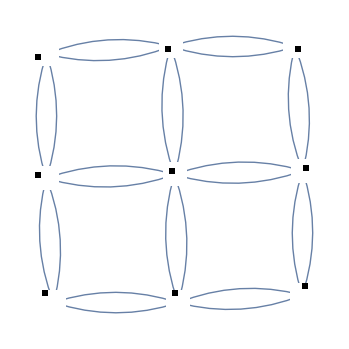

```mathematica
Graph[vertices, allEdges, VertexShapeFunction->(Inset[ArrayPlot[
ReplacePart[ConstantArray[0,{4, 4}],
#2->1]], #1, Center, 10*#3]&)]
```

```mathematica
Table[i, {i, Reverse[Range[4]]}]
```

{4,3,2,1}

```mathematica
rules = {1->2, 2->3, 3->2, 2->1}
```

```mathematica
Reverse[Range[4][[2;;]]]
```

{4,3,2}

```mathematica
getRules[size_]:=Join[Table[i->i+1, {i, size- 1}], Table[i->i - 1, {i, Reverse[Range[size][[2;;]]]}]]
```

```mathematica
getRules[4]
```

{1→2,2→3,3→4,4→3,3→2,2→1}

```mathematica
getRules[size_]:= Table[]
```

```mathematica
getMove[idx_]:= Select[Replace[idx, #]&/@ rules, #!=idx&]
```

```mathematica
getMoves[{i_, j_}]:= Join[Map[{#, j}&, getMove[i]], Map[{i, #}&, getMove[j]]]
```

```mathematica
getAllMoves[posList_, level_]:= Map[getMoves, posList, {level}]
```

```mathematica
getMovesList[init_, maxLevel_]:= Module[{level, movesList, currMoves, nextMoves},
movesList = {init};
currMoves = init;
level = 1;
While[level<=maxLevel,
nextMoves = getAllMoves[currMoves, level];
AppendTo[movesList, nextMoves];
level+=1;
currMoves = nextMoves;
];
movesList
]
```

```mathematica
getMovesList[{{1, 1}}, 3]
```

{{{1,1}},{{{2,1},{1,2}}},{{{{3,1},{1,1},{2,2}},{{2,2},{1,3},{1,1}}}},{{{{{2,1},{3,2}},{{2,1},{1,2}},{{3,2},{1,2},{2,3},{2,1}}},{{{3,2},{1,2},{2,3},{2,1}},{{2,3},{1,2}},{{2,1},{1,2}}}}}}

```mathematica
getMovesList[{{1, 1}}, 2]
```

{{{{2,1},{1,2}}}}

{{{{2,1},{1,2}}},{{}}}

{{{{2,1},{1,2}}},{{}}}

```mathematica
getMoves[1, 1]
```

{{2,1},{1,2}}

```mathematica
getAllMoves[moves_]:=Catenate[getMoves[#[[1]], #[[2]]]&/@ moves]
```

```mathematica
getAllMovesAllPos[allMoves_]:=getAllMoves/@ allMoves
```

```mathematica
path = NestList[getAllMovesAllPos, {{{1, 1}}}, 3];
```

```mathematica
board = ConstantArray[0, {3, 3}]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
path
```

{{{{1,1}}},{{{2,1},{1,2}}},{{{3,1},{1,1},{2,2},{2,2},{1,3},{1,1}}},{{{2,1},{3,2},{2,1},{1,2},{3,2},{1,2},{2,3},{2,1},{3,2},{1,2},{2,3},{2,1},{2,3},{1,2},{2,1},{1,2}}}}

```mathematica
getEdges =
```

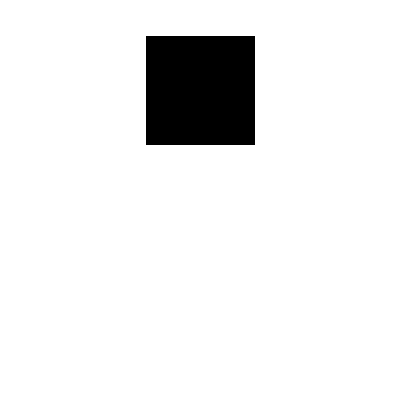

```mathematica
ArrayPlot[ReplacePart[board, t2->1]]
```

```mathematica
getMoves[2, 2]
```

{{3,2},{1,2},{2,3},{2,1}}

```mathematica
moves = Select[Replace[1, #]&/@ rules, #!=1&]
```

{2}

```mathematica
Rule[2, 3]
```

2→3

```mathematica
ReplaceList[1, rules]
```

{2}

```mathematica
ReplaceRepeated[rules]
```

```mathematica
{2->1, 2->3, 1->3}
```

{2→1,2→3,1→3}

```mathematica
Replace[2,#]&/@ rules
```

{1,3,2}

```mathematica
ReplaceAll
```

```mathematica
NearestNeighborGraph[Position[
Table[Mod[i+j+1,2],{i,1,4},{j,1,4}],
1],{All,Sqrt[2]},
VertexSize->1,PerformanceGoal->"Quality",
VertexShapeFunction->(Inset[{{"[◼]", "CheckersGraphic"}}[
ReplacePart[ConstantArray[0,{4,4}],
#2->1],FontSize->8],#1,Center,#3]&),DirectedEdges->True,EdgeStyle->Gray,GraphLayout->"LayeredEmbedding",VertexCoordinates->Automatic]
```

-Graphics-

```mathematica
spaces = Table[{i, j}, {i, 1, 3}, {j, 1, 3}]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}}}

```mathematica
Flatten[spaces, 1]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

```mathematica
spaces
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}}}

```mathematica
states =ReplacePart[ConstantArray[0,{3,3}],
#->1]&/@ Flatten[spaces, 1]
```

{{{1,0,0},{0,0,0},{0,0,0}},{{0,1,0},{0,0,0},{0,0,0}},{{0,0,1},{0,0,0},{0,0,0}},{{0,0,0},{1,0,0},{0,0,0}},{{0,0,0},{0,1,0},{0,0,0}},{{0,0,0},{0,0,1},{0,0,0}},{{0,0,0},{0,0,0},{1,0,0}},{{0,0,0},{0,0,0},{0,1,0}},{{0,0,0},{0,0,0},{0,0,1}}}

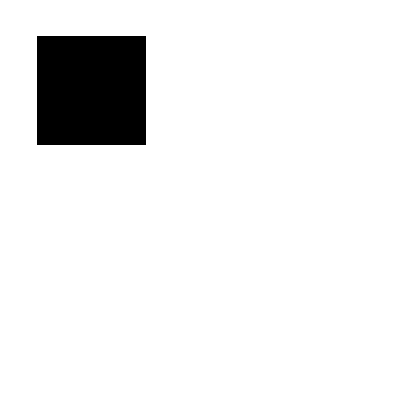
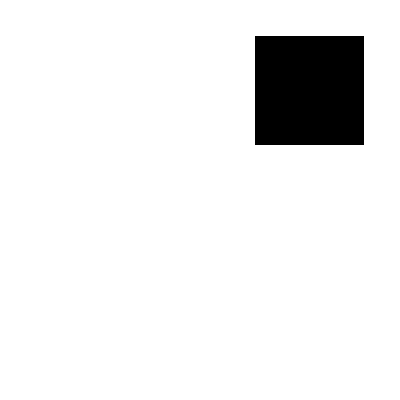
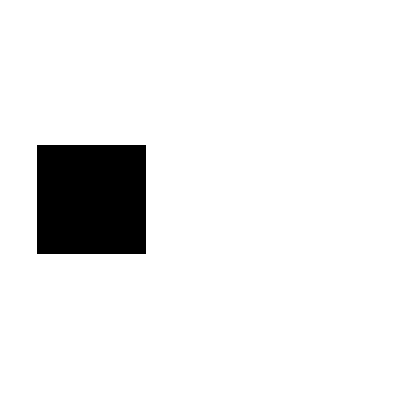
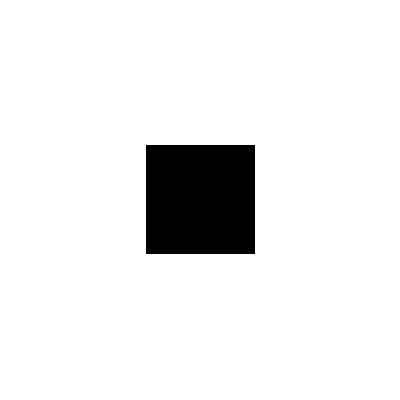
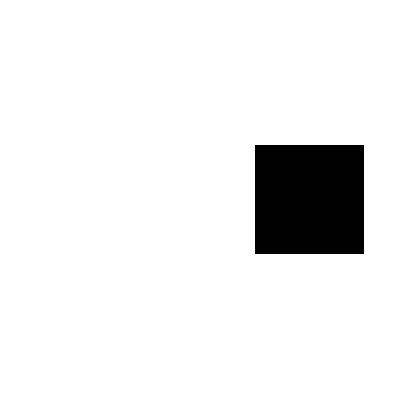
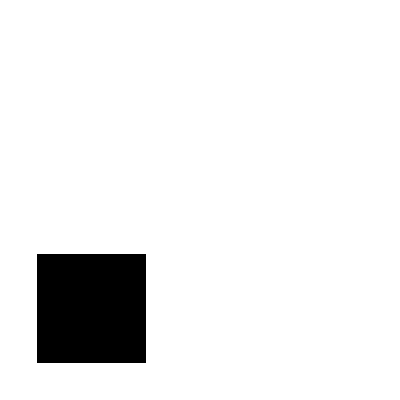
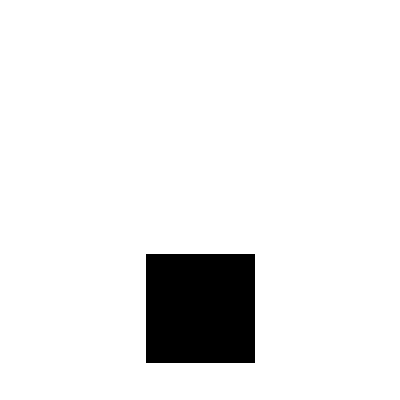
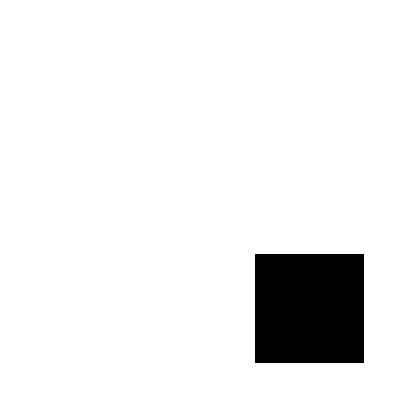
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plots = ArrayPlot/@ states
```

```mathematica
NearestNeighborGraph[plots]
```

NearestNeighborGraph[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]